```mathematica
squreMean[list_List]:=Mean[list]^2;
```

```mathematica
squreMean[{a,b,c,d}]
```

1/16 (a+b+c+d)^2

```mathematica
MemoryInUse[]
```

```mathematica
stressesLong=Import["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/stressNVT_N1024_p3.800_T0.01000000_t1000000000_0.csv","CSV"][[1]]*1024;
```

```mathematica
inGsLong=Import["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/insGNVT_N1024_p3.800_T0.01000000_t1000000000_0.csv","CSV"][[1]];
```

```mathematica
ts=Table[Round[10^(1+0.2t)],{t,0,20}]
```

{10,16,25,40,63,100,158,251,398,631,1000,1585,2512,3981,6310,10000,15849,25119,39811,63096,100000}

```mathematica
meanStress=Table[Mean[MovingMap[squreMean,stressesLong[[1;;100000]],Quantity[ts[[t]],"Events"]]],{t,Length[ts]}];
```

```mathematica
Log10[meanStress/1024/0.01]
```

{-1.04533,-1.12081,-1.20736,-1.3236,-1.46361,-1.629,-1.81058,-2.0056,-2.1778,-2.34055,-2.49788,-2.65585,-2.81666,-2.97138,-3.13934,-3.34918,-3.66938,-3.98537,-4.60091,-4.69325,-5.33293}

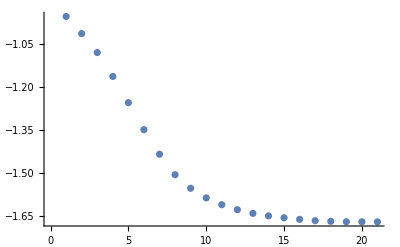

```mathematica
ListPlot[Log10[meanStress/1024/0.01+0.02139801161017213]]
```

```mathematica
(Mean[inGsLong]-Mean[stressesLong^2]/0.01)/1024
```

0.021398

```mathematica
0.02139801161017213+
```

```mathematica
Mean[stressesLong[[1;;Length[stressesLong];;10]]]
```

0.00148808

```mathematica
Length[stressesLong]
```

10000000

```mathematica
Log10[Mean[inGsLong]/1024]
```

-0.556935

```mathematica
Log10[Variance[stressesLong]/1024/0.01]
```

-0.591801

```mathematica
Mean[MovingMap[Variance,stressesLong,Quantity[1000000,"Events"]]]
```

```mathematica
Log10[Mean[MovingMap[Variance,stressesLong,Quantity[1000000,"Events"]]]/1024/0.01]
```

$Aborted

```mathematica
Log10[Variance[stressesLong[[1;;Length[stressesLong];;1000]]]/1024/0.01]
```

-0.582352

```mathematica
{1,2,3,4,5,6,7,8,9}[[2;;9;;5]]
```

{2,7}

```mathematica
stresses=Table[Mean[Table[Variance[stressesLong[[ini;;Length[stressesLong];;t]]],{ini,t}]],{t,{10,100,1000,10000,100000}}]
```

{2.62119,2.62119,2.6212,2.62121,2.62128}

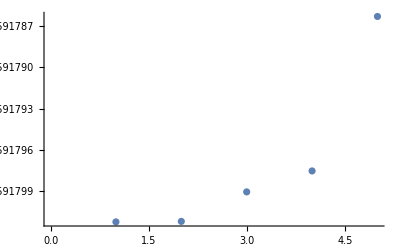

```mathematica
ListPlot[Log10[stresses/1024/0.01]]
```

```mathematica
meanStress=Table[Mean[Table[Mean[stressesLong[[ini;;Length[stressesLong];;t]]],{ini,t}]],{t,{10,100,1000,10000,100000}}]
```

{0.000390604,0.000390604,0.000390604,0.000390604,0.000390604}

```mathematica
dataSubset=Import["/home/chengling/Research/Project/Cell/AnalyticalG/data/N100/derivativeTest/nvt_N100_p3.800_T0.15000000_0.nc",{"Data","position",{9131503}}]
```

Import::noelem: The Import element "9131503" is not present when importing as NetCDF.

$Failed

```mathematica
data=Import["/home/chengling/Research/Project/Cell/AnalyticalG/data/N100/derivativeTest/nvt_N100_p3.850_T0.01000000_0.nc",{"Data",{[[1,1]]}}]
```

```mathematica
stress=Normal[Flatten[data[[5]]]];
```

```mathematica
id=Position[stress,Max[stress]][[1,1]]
```

9131503

```mathematica
Max[stress]
```

3489.83

## Analytical functions

```mathematica
(*Cross product for 2d vectors*)
Cross2d[r1_,r2_]:=r1[[1]]r2[[2]]-r1[[2]]r2[[1]]
(*The vertex position given the three adjecent cell positions*)
voro[ri_,rj_,rk_]:=Module[{rij,rjk,rik,cross,d,α,β,γ},
rij=ri-rj;
rjk=rj-rk;
rik=ri-rk;

cross=Cross2d[rij,rjk];
d=2*cross*cross;

α=(rjk.rjk)*(rij.rik)/d;
β=-(rik.rik)*(rij.rjk)/d;
γ=(rij.rij)*(rik.rjk)/d;

α*ri+β*rj+γ*rk
];
```

```mathematica
(*calculate perimetes and areas given the positions of all the vertices*)
peri[hv_List]:=Sum[Sqrt[(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]).(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]])],{i,1,Length[hv]}];

area[hv_List]:=Sum[0.5*Cross2d[hv[[i]],hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]],{i,1,Length[hv]}];
```

```mathematica
(*This is the 1st derivative of e w.r.t. h*)
dedhGeneral[hv_List,KA_,KP_,PA_,PP_]:=Module[{dedhx,dedhy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
dedhx=(-1. hiLasty+1. hiNexty) KA (a-PA)+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
dedhy=(-1. hiLastx+1. hiNextx) KA (PA-a)+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
{dedhx,dedhy}
]
```

```mathematica
(*This is the generalized function for de2dhidhj*)

de2dhihjxx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xx=2 ((-0.5 hiLasty+0.5 hiNexty)^2 KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLastx+hix)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNextx+hix)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2xx=2 ((-0.5 hiy+0.5 hjNexty) (-0.5 hiLasty+0.5 hjy) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[j==Length[hv],
de2xx=2 ((0.5 hiy-0.5 hjLasty) (0.5 hiNexty-0.5 hjy) KA+((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2xx=2 (-0.5 hiLasty+0.5 hiNexty) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xx
];
de2dhihjxy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xy=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2xy=2 (0.5 hix-0.5 hjNextx) (-0.5 hiLasty+0.5 hjy) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP- KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2xy=2 (-0.5 hix+0.5 hjLastx) (0.5 hiNexty-0.5 hjy) KA+2 ((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP+KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2xy=2 (-0.5 hiLasty+0.5 hiNexty) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xy
];
de2dhihjyx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yx=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2yx=2 (-0.5 hiy+0.5 hjNexty) (0.5 hiLastx-0.5 hjx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP+ KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2yx=2 (0.5 hiy-0.5 hjLasty) (-0.5 hiNextx+0.5 hjx) KA+2 ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) ((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) KP-KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2yx=2 (0.5 hiLastx-0.5 hiNextx) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yx
];
de2dhihjyy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yy=2 ((-0.5 hiLastx+0.5 hiNextx)^2 KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLasty+hiy)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNexty+hiy)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2yy=2 ((0.5 hix-0.5 hjNextx) (0.5 hiLastx-0.5 hjx) KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[j==Length[hv],
de2yy=2 ((-0.5 hix+0.5 hjLastx) (-0.5 hiNextx+0.5 hjx) KA+((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2yy=2 (0.5 hiLastx-0.5 hiNextx) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yy
];
de2dhdhGeneral[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{},
{{de2dhihjxx[hv,j,KA,KP,PA,PP],de2dhihjxy[hv,j,KA,KP,PA,PP]},{de2dhihjyx[hv,j,KA,KP,PA,PP],de2dhihjyy[hv,j,KA,KP,PA,PP]}}
]
```

```mathematica
(*These are the analytical forms for dhdgamma and d2hdgamma2*)
dhdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(r1x r1y (r2y-r3y)+r2y (r2x-r3x) r3y+r1y (-r2x r2y+r3x r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-2 r2x r2y r3x+r2y r3x^2-r2x^2 r3y-r2y^2 r3y+2 r2x r3x r3y+r2y r3y^2+r1x^2 (-r2y+r3y)+r1y^2 (-r2y+r3y)+2 r1x (r2x r2y+r1y (-r2x+r3x)-r3x r3y)+r1y (r2x^2+r2y^2-r3x^2-r3y^2))/(2 (-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y))}
];
d2hdgdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{((r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-r2y^2 r3x+r1y^2 (-r2x+r3x)-2 r2x r2y r3y+2 r2y r3x r3y+r2x r3y^2+r1x (r2y^2-r3y^2)+2 r1y (r2x r2y-r3x r3y+r1x (-r2y+r3y)))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y)}
];
```

```mathematica
(*Now this is to calculate de2dgammadgamma for cell i*)
d2eidgdgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[Sum[de2dhdhGeneral[RotateLeft[vList,i],j,KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[j+i==Length[vList],Length[vList],Mod[j+i,Length[vList]]]]]]],allPoints[[neilist[[If[j+1+i==Length[vList]||j+1+i==2*Length[vList],Length[vList],Mod[j+1+i,Length[vList]]]]]]]].dhdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{j,1,Length[vList]}]+dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].d2hdgdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*Now this is to calculate dedgamma for cell i*)
deidgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[i+1==Length[vList],Length[vList],Mod[i+1,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList]||2+i==2*Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*This gives the neighbor list of cell i in a counterclock-wise order and this neighbor list aligns with the vertex id list*)
```

```mathematica
reorderCCWIndices[centerIndex_,neighborIndices_List,allPoints_]:=Module[{center,neighbors,angles,sortedIndices},center=allPoints[[centerIndex]];
neighbors=allPoints[[neighborIndices]];
angles=ArcTan@@@(#-center&/@neighbors);
sortedIndices=Ordering[angles];
neighborIndices[[sortedIndices]]
(*Table[neighborIndices[[FirstPosition[sortedIndices,i][[1]]]],{i,1,Length[neighborIndices]}]*)];
neighborListRightOrder[i_,voronoiPolygons_List,cellIndex_,allPoints_]:=Module[{trianglesWithCenteri,neighborListRandomOrder,neighborListCCWOrder,delaunay,vetices,firstVerticeID},
delaunay=DelaunayMesh[allPoints];
trianglesWithCenteri=Select[First/@MeshCells[delaunay,2],MemberQ[#,i]&];
neighborListRandomOrder=DeleteCases[Union[Flatten[trianglesWithCenteri]],i];
neighborListCCWOrder=reorderCCWIndices[i,neighborListRandomOrder,allPoints];
vetices=Table[voro[allPoints[[i]],allPoints[[neighborListCCWOrder[[j]]]],allPoints[[neighborListCCWOrder[[If[j+1==Length[neighborListCCWOrder],Length[neighborListCCWOrder],Mod[j+1,Length[neighborListCCWOrder]]]]]]]],{j,1,Length[neighborListCCWOrder]}];
firstVerticeID=Nearest[vetices->Automatic,voronoiPolygons[[cellIndex[[i]]]][[1]][[1]]][[1]];
RotateLeft[neighborListCCWOrder,firstVerticeID-1]
];
```

```mathematica
(*This is the function that returns a list of dei/dg and d2ei/dg2 for each cell*)
AnalyticalCell[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Table[{deidgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidgdgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

```mathematica
AnalyticalCellTest[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Table[{deidgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidgdgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

## Numerical function:

```mathematica
getData[fname_]:=Module[{t,n,frames,types,times,positions,posSet},
t=Import[fname,"Data"];
n=Length[t[[8,1]]]/2;
frames=Length[t[[2]]];
times=Flatten[t[[2]]];
positions={};
Do[
posSet=t[[8,fr]];
AppendTo[positions,Table[{posSet[[2*i+1]],posSet[[2*i+2]]},{i,0,n-1}]];
,{fr,1,frames}];
{n,frames,positions,types,times}];
```

```mathematica
(*This function returns dei/dg and d2ei/dg^2 for each cell*)
```

```mathematica
numdericalCell[allPoints_List,box_List,ddx_,ka_,kp_,pa_,pp_]:=Module[{Vareas0,Vperis0,Vareas1,Vperis1,VareasI,VperisI,copies,translations,translatedCopies,allPointsPBD,cellIndex,cellIndex0,cellIndex1,strainfor,strainback,vm,vm1,vm0,allPointsPBD0,allPointsPBD1,min,max,voronoiPolygons,voronoiPolygons1,voronoiPolygons0},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
strainfor={{1,ddx},{0,1}};
strainback={{1,-ddx},{0,1}};
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD0=strainfor.#&/@allPointsPBD;
vm0=VoronoiMesh[allPointsPBD0,{{min,max},{min,max}}];
voronoiPolygons0=MeshPrimitives[vm0,2];
cellIndex0=Table[Position[Table[RegionMember[voronoiPolygons0[[j]],allPointsPBD0[[i]]],{j,Length[allPointsPBD0]}],True][[1,1]],{i,Length[allPoints]}];
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD1=strainback.#&/@allPointsPBD;
vm1=VoronoiMesh[allPointsPBD1,{{min+0.001*min,max+0.001*max},{min,max}}];
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
voronoiPolygons1=MeshPrimitives[vm1,2];
cellIndex1=Table[Position[Table[RegionMember[voronoiPolygons1[[j]],allPointsPBD1[[i]]],{j,Length[allPointsPBD1]}],True][[1,1]],{i,Length[allPoints]}];
Table[{(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2-ka(Vareas1[[cellIndex1[[i]]]]-pa)^2-kp(Vperis1[[cellIndex1[[i]]]]-pp)^2)/(2*ddx),(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2+ka(Vareas1[[cellIndex1[[i]]]]-pa)^2+kp(Vperis1[[cellIndex1[[i]]]]-pp)^2-2*(ka(VareasI[[cellIndex[[i]]]]-pa)^2+kp(VperisI[[cellIndex[[i]]]]-pp)^2))/ddx/ddx},{i,1,Length[allPoints]}]
];
```

```mathematica
positions=Table[{data[[4,id]][[2*i+1]],data[[4,id]][[2*i+2]]},{i,0,99}];
```

```mathematica
num=numdericalCell[positions,{10,10},0.0001,1,1,1,3.80]
```

{{0.078608,0.775043},{0.00343828,4.01898},{0.0662071,0.464621},{0.0307938,0.389543},{0.377935,3.11592},{0.00999864,0.149603},{0.0954984,0.108112},{-0.0188182,0.310151},{-0.0500832,-0.0160892},{0.0242063,0.498099},{-0.303661,2.27602},{0.0213024,0.212075},{-0.0221793,0.711309},{-0.431284,0.919359},{0.0228782,0.716662},{0.0524385,-0.772256},{0.000863603,0.308385},{-0.187276,1.2717},{0.797139,4.35693},{0.0450631,0.951643},{0.0615587,-0.20998},{0.166892,1.55483},{-0.0663893,-0.259786},{0.0439064,0.216056},{0.395491,1.73734},{-0.0811726,2.42414},{0.122823,-0.226116},{0.0505309,-0.21324},{0.00879063,-0.0640225},{0.0239676,-0.0101563},{-0.0549853,0.444212},{0.0299855,0.848635},{0.381991,2.88068},{-0.0309501,0.525385},{0.704929,-1.44058},{0.360236,-0.539954},{0.438982,1.12289},{-0.242684,0.0776834},{0.0128485,0.133695},{-0.146828,-0.84671},{-0.248555,1.54631},{0.394819,2.44194},{-0.0671152,0.653988},{0.0647164,-0.336837},{0.0495908,0.616895},{0.0155875,0.22375},{0.0302362,0.556254},{-0.0323657,0.961991},{0.352209,1.51184},{0.0241148,0.482502},{0.0598813,0.724617},{-0.150016,1.37273},{-0.064247,0.159261},{0.152677,1.34143},{0.0955992,1.18983},{1.06493,4.81924},{0.588257,1.78039},{-0.39578,3.00872},{0.0367014,2.04003},{0.0422394,0.773236},{0.219317,0.973838},{0.336028,2.02197},{-0.0341612,0.522382},{-0.202379,0.93239},{0.422798,3.30846},{0.168213,-0.242905},{0.0526789,0.254706},{-0.104793,0.127086},{-0.0796097,0.642717},{0.130423,0.504474},{-0.0127773,0.772312},{0.266164,-0.0571021},{0.0917002,1.04039},{-0.222884,2.58544},{0.00997271,0.141233},{0.425068,0.692659},{-0.25986,-0.251468},{-0.107757,0.210073},{-0.153047,2.28978},{-0.176776,1.6661},{-0.216524,1.11079},{0.586512,3.66},{-0.126709,1.09844},{-0.0651761,0.915196},{0.0474332,0.388178},{0.0375914,0.318085},{0.0725347,1.23835},{0.116119,-1.12334},{0.204353,1.10359},{-0.101392,2.1082},{-0.124681,1.14421},{0.0294043,0.32223},{-1.1873,3.67184},{-0.107271,0.591577},{0.421762,2.31264},{0.51466,-0.0313721},{0.103012,1.25648},{0.026568,1.64572},{0.14011,2.20203},{0.230904,1.7991}}